```mathematica
SetDirectory[NotebookDirectory[]]
<<"functions.m"
```

/home/zuxian/Documents/BAE

```mathematica
(* ::Package:: *)

(* SU(N) XXX nested Bethe equations (periodic, homogeneous, zero twist) *)
ClearAll[u, BetheVariablesSUN, BetheEquationsSUN,
  selfProd, lowerProd, upperProd];

(* All unknown rapidities u[a,k] in a flat list, ordered by levels *)
BetheVariablesSUN[M_List] :=
  Flatten @ Table[u[a, k], {a, 1, Length[M]}, {k, 1, M[[a]]}];

(* helper products *)
selfProd[a_Integer, k_Integer, M_List] :=
  Times @@ Table[
    If[j == k, 1, (u[a, k] - u[a, j] + I)/(u[a, k] - u[a, j] - I)],
    {j, 1, M[[a]]}
  ];

lowerProd[1, k_Integer, M_List] := 1;
lowerProd[a_Integer?Positive, k_Integer, M_List] /; a > 1 :=
  Times @@ Table[
    (u[a, k] - u[a - 1, j] - I/2)/(u[a, k] - u[a - 1, j] + I/2),
    {j, 1, M[[a - 1]]}
  ];

upperProd[a_Integer, k_Integer, M_List] /; a < Length[M] :=
  Times @@ Table[
    (u[a, k] - u[a + 1, j] - I/2)/(u[a, k] - u[a + 1, j] + I/2),
    {j, 1, M[[a + 1]]}
  ];
upperProd[a_Integer, k_Integer, M_List] /; a == Length[M] := 1;

Options[BetheEquationsSUN] = {"Form" -> "multiplicative"};  (* or "log" *)
BetheEquationsSUN[L_Integer?Positive, M_List?VectorQ, OptionsPattern[]] :=
 Module[{Nlev = Length[M], eqMult},
  
  (* multiplicative equations, exactly as in your text *)
  eqMult =
    Flatten @ Table[
      Which[
        a == 1, (* level a = 1 *)
        Table[
          ((u[1, k] + I/2)/(u[1, k] - I/2))^L ==
            selfProd[1, k, M] * upperProd[1, k, M],
          {k, 1, M[[1]]}
        ],
        
        1 < a < Nlev, (* levels a = 2..N-2 *)
        Table[
          1 == lowerProd[a, k, M] * selfProd[a, k, M] * upperProd[a, k, M],
          {k, 1, M[[a]]}
        ],
        
        a == Nlev, (* top level a = N-1 *)
        Table[
          1 == lowerProd[a, k, M] * selfProd[a, k, M],
          {k, 1, M[[a]]}
        ]
      ],
      {a, 1, Nlev}
    ];
  
  <|
    "Equations"   -> eqMult,
    "Variables"   -> BetheVariablesSUN[M],
    "LevelCounts" -> M
  |>
]
```

```mathematica
Unprotect[M];
yd ={4,2,1};
data421 = LoadBAEResults[yd];
(* Example: SU(3) sector with L = 6 and magnon numbers M = {2, 1} *)
L  = Total@yd;
M  = Drop[Drop[AugmentedYoungD[yd][[All,1]],1],-1]

pack = BetheEquationsSUN[L, M];          (* multiplicative form *)
eqs  = pack["Equations"];
vars = pack["Variables"];

eqs // Column
vars
```

{3,1}

(ⅈ/2+u[1,1])^7/(-ⅈ/2+u[1,1])^7==((ⅈ+u[1,1]-u[1,2]) (ⅈ+u[1,1]-u[1,3]) (-ⅈ/2+u[1,1]-u[2,1]))/((-ⅈ+u[1,1]-u[1,2]) (-ⅈ+u[1,1]-u[1,3]) (ⅈ/2+u[1,1]-u[2,1]))
(ⅈ/2+u[1,2])^7/(-ⅈ/2+u[1,2])^7==((ⅈ-u[1,1]+u[1,2]) (ⅈ+u[1,2]-u[1,3]) (-ⅈ/2+u[1,2]-u[2,1]))/((-ⅈ-u[1,1]+u[1,2]) (-ⅈ+u[1,2]-u[1,3]) (ⅈ/2+u[1,2]-u[2,1]))
(ⅈ/2+u[1,3])^7/(-ⅈ/2+u[1,3])^7==((ⅈ-u[1,1]+u[1,3]) (ⅈ-u[1,2]+u[1,3]) (-ⅈ/2+u[1,3]-u[2,1]))/((-ⅈ-u[1,1]+u[1,3]) (-ⅈ-u[1,2]+u[1,3]) (ⅈ/2+u[1,3]-u[2,1]))
1==((-ⅈ/2-u[1,1]+u[2,1]) (-ⅈ/2-u[1,2]+u[2,1]) (-ⅈ/2-u[1,3]+u[2,1]))/((ⅈ/2-u[1,1]+u[2,1]) (ⅈ/2-u[1,2]+u[2,1]) (ⅈ/2-u[1,3]+u[2,1]))

{u[1,1],u[1,2],u[1,3],u[2,1]}

```mathematica
solindex=21;
myinitvar=Table[RandomReal[],{j,Length@vars}];
myinitvar=data421[["DataBethe"]][[solindex]]//Flatten;
initialGuess = Transpose[{vars,myinitvar}];
```

```mathematica
perturb[z_]:=If[Im[z]!=0,z+I 10^-12 RandomReal[{-1,1}],z];
myinitvar=Table[RandomReal[],{j,Length@vars}];
myinitvar=(data421[["DataString"]][[solindex]]//Flatten);
initialGuess =Transpose[{vars,perturb/@myinitvar}];
```

```mathematica
eqs0=(eqs/. (lhs_==rhs_):>(lhs-rhs));  (*residuals*)
sol=FindRoot[eqs0,initialGuess,AccuracyGoal->30,PrecisionGoal->30,MaxIterations->500];
```

{0,0,0,0}

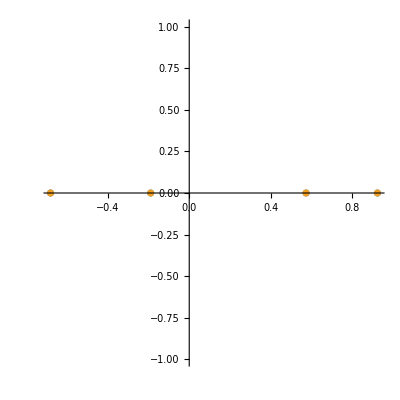

```mathematica
eqs0/.sol//Chop
ComplexListPlot[{sol//Values,data421[["DataBethe"]][[solindex]]//Flatten},AspectRatio->1,PlotRange->All]
```